# Metropolis Hastings Algorithm

A brief description of the Metropolis Hastings Monte Carlo Markov Chain Algorithm with examples.

## Frequentist Approach to Inference

In a frequentist approach, data is random and the parameters are fixed. Inference is determined by finding parameters that maximize Likelihood.
If we have some data 𝒟 and a model with parameters, θ, then the Likelihood function, L(θ|𝒟), is defined in terms of the parameters of the probability density, P(𝒟|θ). 

L(θ|𝒟) = P(𝒟|θ)

P(𝒟|θ) (often ln(P(𝒟|θ)) for ease of calculation) is maximized to infer the parameters θ for which the probability of attaining the data 𝒟 is highest.

For example, let’s consider a biased coin. Let ‘p’ be the probability of getting heads and (1-p) is the probability of getting tails. 
Let’s say we toss the coin 20 times and we get 14 heads. A frequentist will calculate the Maximum Likelihood estimate of ‘p’ as follows,

```mathematica
p=14/20//N
```

0.7

Formally, we can compute the Maximum Likelihood Estimate using the Binomial Distribution as follows:

```mathematica
f[x_]:=Binomial[20,14]*x^14 * ((1-x)^6)
```

Let’s now plot this function:

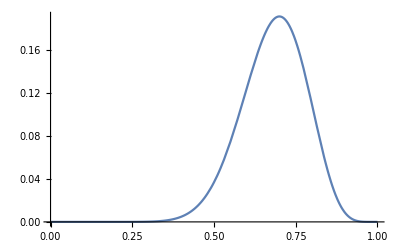

```mathematica
Plot[f[y],{y,0,1}]
```

Now let’s find the maximum of this curve:

```mathematica
FindMaximum[f[y],{y,0,1}]
```

{0.191639,{y→0.7}}

We see that the maxima occurs at y=0.7. This is equal to the the value ‘p’ we calculated before.

The probability of getting ‘n’ heads in ‘n’ coin tosses will be p^n:

```mathematica
p^n
```

0.7^n

So, the probability of getting two heads in 2 coin tosses is,

```mathematica
p^2
```

0.49

### Bayesian Approach to Inference

In the Bayesian approach, the data 𝒟 is considered to be fixed and the parameters, θ, are variable. Inference is performed by maximizing the posterior probability, f(θ|𝒟).
This posterior distribution is defined using the Bayes Rule as,

f(θ|𝒟) =  f(𝒟|θ)f(θ)/f(𝒟)

where,

f(𝒟|θ) = Likelihood function
 f(θ) = Prior Probability
 f(θ|𝒟) = Posterior Probability
 f(𝒟) = Marginal Probability = ∫_θ f(𝒟|θ)f(𝒟)ⅆθ

The prior probability signifies the prior belief regarding the posterior distribution. The prior probability can have a large effect on the posterior probability and thus, care must be taken before picking one.

Let’s now see how Bayesian inference works in the same example we saw in the previous section - A biased coin is tossed 20 times and we get heads 14 times. A Bayesian will treat the data to be fixed and the probability ‘p’ to be a random variable with its own distribution. 

In the Bayes Rule, we see that the denominator f(𝒟) is constant so, the posterior distribution, f(θ|𝒟) ∝ f(𝒟|θ) f(θ). A very convenient prior distribution to use for the Binomial Distribution is the Beta distribution which is also known as the conjugate prior of the Binomial Distribution. The Uniform Distribution is an instance of a Beta distribution with the parameters, a =1 and b = 1. Let’s use a Uniform prior distribution here which basically means that we have no prior belief in the distribution of the posterior density function.

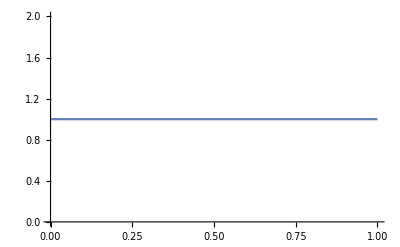

```mathematica
Plot[PDF[BetaDistribution[1,1],x],{x,0,1}]
```

We know the likelihood function, f(𝒟|θ) = f(𝒟|p) :

```mathematica
Clear[f]
f[x_]:=Binomial[20,14]*x^14*((1-x)^6)
```

Let’s now plot the function, g(p|𝒟) = f(𝒟|p) f(p) ∝ f(p|𝒟):

```mathematica
Clear[g]
g[x_]:=PDF[BetaDistribution[1,1],x] * f[x]
Plot[g[x],{x,0,1}]
```

-Graphics-

Let’s now find the maximum of this function.

```mathematica
FindMaximum[g[y],{y,0,1}]
```

{0.191639,{y→0.7}}

So we find that the probability of getting heads here is p=0.7.

Let's now compute the probability of getting 2 heads in a row. 
f(HH|𝒟) =∫_0^1 f(HH|p)f(p|𝒟)ⅆp 
We know that, f(HH|p) = p^2.
f(p|𝒟) from Line[56] is g(p|𝒟)/∫_0^1 g(p|𝒟)ⅆp:

```mathematica
g2[x_]:=PDF[BetaDistribution[1,1],x] * f[x]
f2[x_]:=g[x]/Integrate[g2[y],{y,0,1}]
```

```mathematica
posteriorProbability=Integrate[f2[x]*x^2,{x,0,1}]//N
```

0.474308

The frequentist approach gives us a probability of 0.49 but the Bayesian approach gives us a probability of 0.47. This example illustrates the difference between the two inference methods.

The Marginal probability, in real problems, is often hard to compute since it involves integration over all the parameters in the model. These integrals are often intractable. In order to ease this computation, Monte Carlo Markov Chain techniques are used to sample the distribution without the need to compute such complex integrals. 

Before getting into the algorithm, lets briefly go over what a Markov Chain is in the next section.

### What is a Markov Chain?

A Markov chain is any stochastic process in which the next state of the system depends only on the current state. This property is formally called the Markov Property. 

A Markov process is defined by a transition matrix which shows the probability of moving from one state to another. Shown below is a simple transition matrix for four states, "1", "2", "3", "4":

```mathematica
t = {{0, 1/2, 0, 1/2}, {1/2, 0, 0, 1/2}, {1/2, 0, 0, 1/2}, {0, 1/2, 1/2, 0}};
t // MatrixForm
```

(0 | 1/2 | 0 | 1/2
1/2 | 0 | 0 | 1/2
1/2 | 0 | 0 | 1/2
0 | 1/2 | 1/2 | 0)

Here is the corresponding Markov Chain:

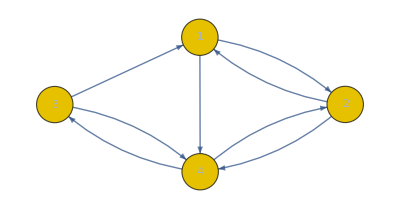

```mathematica
proc = DiscreteMarkovProcess[3, t];
Graph[proc]
```

There are two types of Markov Chains, discrete-time and continuous-time based on, as the name suggests, if the state of the system is defined in a discrete time indices or in continuous time.

### The Algorithm

To illustrate how the algorithm functions, it will be easiest to go an example first.

Lets consider a Normal Distribution as an example. In reality, since the distribution is in closed form expression there would be no need to use the MH algorithm to sample it but lets use it as an example here. 

Let’s say we have data that is distributed in the form of a normal distribution. We want to sample this distribution. 
Let take a Normal distribution with mean, μ =1 and standard deviation, σ=1, to be our posterior distribution:

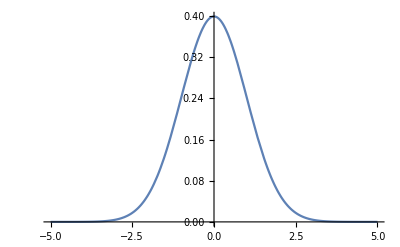

```mathematica
posterior = NormalDistribution[0, 1];
Plot[PDF[posterior, x], {x, -5, 5}]
```

Our Likelihood function will be as follows:

```mathematica
Likelihood[posterior, {x}]
```

(ⅇ^(-x^2/2))/(√(2 π))

(ⅇ^(-x^2/2))/(√(2 π))

For our prior probability distribution, let’s consider a Uniform distribution which is an uninformative prior i.e., it does not reinforce any prior belief we have in the distribution. If no knowledge of the final distribution is known, it is safer to use an uninformative prior like the Uniform Distribution or Jeffreys prior.

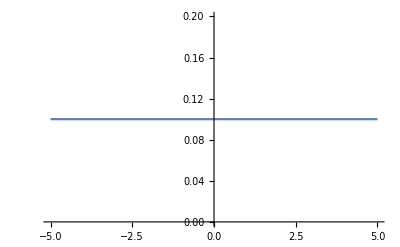

```mathematica
prior = UniformDistribution[{-5, 5}];
Plot[PDF[prior, x], {x, -5, 5}]
```

Let’s pick a random starting parameter, θ1 for state 1

```mathematica
θ1=RandomReal[]
```

0.484393

Let’s now choose a parameter for state 2 by randomly sampling a “proposal distribution”. This is where the algorithm incorporates the Markov Chain. This proposal distribution will be used to choose a new parameter to determine a new state for the system. In the steps further, we will see how to set the probability of the system moving to the new state. 

A usual proposal density that can be chosen is a Normal Distribution with the mean set as the parameter in the present state and a constant standard deviation.

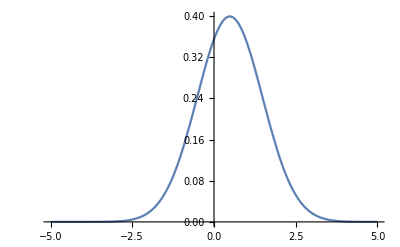

```mathematica
proposal = NormalDistribution[θ1, 1];
Plot[PDF[proposal, x], {x, -5, 5}]
```

Let’s choose a parameter θ2 for state 2.

```mathematica
θ2 = RandomVariate[NormalDistribution[θ1, 1]]
```

-1.21357

Now let’s compute an “acceptance probability” to see if the system will transition from state 1 to state 2. This will be the transition probability of the Markov Chain. Now, if the posterior probability of the system at state 2 is higher than state 1 we definitely want to sample the parameter, θ2 in state 2. On the other hand, if the posterior probability of the system in state 2 is lower than state 1 then we want to jump into state 2 with some probability.

So let’s compute an acceptance probability, α:

```mathematica
α:=((Likelihood[posterior,{θ2}]*PDF[prior,θ2])/MarginalProbability)/((Likelihood[posterior,{θ1}]*PDF[prior,θ1])/MarginalProbability);
```

As you can see Marginal Probability cancels out and hence, we can sample the entire distribution without computing the Marginal Probability(which as discussed before, in more realistic problems, can be computationally infeasible).

```mathematica
α
```

0.538454

Note that probability cannot be greater than 1, let’s restructure α such that the maximum value can only be 1.

```mathematica
α = Min[1,(Likelihood[posterior,{θ2}]*PDF[prior,θ2])/(Likelihood[posterior,{θ1}]*PDF[prior,θ1])]
```

0.538454

This will be the probability with which we determine whether the MCMC will go to the new state. 
To probabilistically make a move from one state to the next, we can generate a random number between 0 and 1 and if the generated number is less than α, then the system will move to the next state else it will remain in the current state.

```mathematica
If[RandomReal[]<α,newState,oldState]
```

oldState

This step is repeated until we get a preset number of states. I’ve incorporated these steps into a function below:

```mathematica
Clear[sampleWithMCMC]
sampleWithMCMC[posteriordist_,priordist_, steps_, init_,proposalDensity_:(NormalDistribution[#,1]&)]:=(
calculatePosterior[x_]:=Likelihood[posteriordist,{x}] * PDF[priordist, x];
moveToNextStep[old_, new_]:= If[calculatePosterior[old]>0,If[RandomReal[] <=Min[1,calculatePosterior[new]/calculatePosterior[old]],new,old],new];
NestWhile[
With[{old=If[Length[#]>0,Last[#],RandomVariate[proposalDensity[init]]]},
new = RandomVariate[proposalDensity[old]];
accepted = moveToNextStep[old,new];
Append[#,accepted]
]&,
{},
Length[#]<steps&
])
```

Now let’s repeat the steps 1000 times to get 1000 samples from the posterior density.

```mathematica
walk=sampleWithMCMC[NormalDistribution[0,1], UniformDistribution[{-5,5}],10000,0,(NormalDistribution[#,1]&)];
```

Here’s a plot showing the prior distribution, posterior distribution and a normalized histogram of the sampled by the MCMC.

```mathematica
l=Plot[{PDF[posterior,x],PDF[prior,x]},{x,-5,5}, PlotRange->{{-5,5},All}, PlotStyle->{Darker[Green],Darker[Red]}, PlotLegends->Placed[{"Posterior Distribution", "Prior Distribution"},Above]];
sh=Histogram[walk,Automatic,"ProbabilityDensity", PlotRange->{{-5,5},All}];
Show[sh,l]
```

-Graphics-

A common tool used to diagnose if the MCMC is running optimally is the “trace” plot. The trace plot is a line plot of the current state of the system over time. Let’s now plot the trace plot of the distribution we just sampled.

```mathematica
ListLinePlot[walk, PlotLabel->"Trace Plot"]
```

-Graphics-

We see from the trace plot that the MCMC is sampling parameters from all regions of the distribution. 
For convenience, let’s combine the function sampleWithMCMC and the commands used to plot into one function:

```mathematica
plotMCMC[posteriordist_,priordist_, steps_, init_, xmin_, xmax_,proposalDensity_:(NormalDistribution[#,1]&)]:=
With[{walk=sampleWithMCMC[posteriordist,priordist, steps,init,proposalDensity]},
l=Plot[{PDF[posteriordist,x],PDF[priordist,x]},{x,xmin,xmax}, PlotRange->{{xmin,xmax},All}, PlotStyle->{Darker[Green],Darker[Red]}, PlotLegends->Placed[{"Posterior Distribution", "Prior Distribution"},Above]];
sh=Histogram[walk,Automatic,"ProbabilityDensity", PlotRange->{{xmin,xmax},All}];
distplot=Show[sh,l];
trace=ListLinePlot[walk, PlotLabel->"Trace Plot"];
GraphicsGrid[{{distplot,trace}}, ImageSize->{600,Automatic}]
]
```

Let’s now run the combined function to repeat the sampling of the posterior distribution and plot the sampled distribution and trace plot:

```mathematica
plotMCMC[NormalDistribution[0,1], UniformDistribution[{-5,5}],10000, 0, -5, 5,(NormalDistribution[#,1]&)]
```

-Graphics-

This is how the Metropolis Hastings algorithm is described formally,

To sample the posterior probability, f(θ|𝒟),

1. Start at initial parameters, θ_0 
2. For i in 1...steps	
	Pick new point, θ_1from the Proposal Density which has θ_0 as a parameter
	Compute g(𝒟|θ_1) = h(θ_1) × Likelihood(θ_1|𝒟) 
	Compute g(𝒟|θ_0) = h(θ_0) × Likelihood(θ_0|𝒟) 
	Calculate acceptance probability, α = min{1, g(𝒟|θ_1)/g(𝒟|θ_0)}
	Accept new state θ_1 with probability α

## Trace Plots

Let’s now change the parameters of the proposal density to see how the trace changes. 
Instead of using σ=1 let’s try σ=100:

```mathematica
plotMCMC[NormalDistribution[0,1], UniformDistribution[{-5,5}],1000, 0,-5, 5,(NormalDistribution[#,100]&)]
```

-Graphics-

We see that the posterior distribution is not sampled very well. We also see in the trace plot above that the MCMC spends a lot of time in just one state since a lot of parameters sampled from the proposal density with a very large standard deviation give a very low transition(acceptance) probability.

Let’s now try sampling the same posterior distribution 10000 times using a different prior distribution. We’ll use a NormalDistribution with μ=3 and σ=1:

```mathematica
plotMCMC[NormalDistribution[0,1], NormalDistribution[3,1],10000,0, -5, 10,(NormalDistribution[#,1]&)]
```

-Graphics-

The posterior distribution plot illustrates the importance of choosing a correct prior distribution. In this plot we see that the MCMC samples only a part of the posterior distribution since our prior distribution in the posterior distribution was misleading. 

Let’s now use a NormalDistribution with μ=0 and σ=1 as our prior distribution:

```mathematica
plotMCMC[NormalDistribution[0,1], NormalDistribution[0,1],10000,0, -5, 5,(NormalDistribution[#,1]&)]
```

-Graphics-

We see here that the posterior distribution reinforced our belief in the prior distribution given that they are exactly the same.

In this way we use the Metropolis Hastings MCMC to sample other distributions as well. 
Let’s try sampling a GammaDistribution with the parameters α=2 and β=1/2 with an Exponential Distribution with μ=2 as the prior and a NormalDistribution as the proposal density:

```mathematica
plotMCMC[GammaDistribution[2,1/2], ExponentialDistribution[2],10000,0, 0, 16,(NormalDistribution[#,1]&)]
```

-Graphics-

## Sampling Multivariate Distributions

Let’s now try sampling a multivariate normal distribution. There are two ways to sample a multi dimensional distribution, Block-wise and Component-wise sampling.

### Block-wise sampling

Let’s sample a Multivariate Normal Distribution with μ={3,2} and a covariance matrix = (4 | 0
0 | 9).

```mathematica
Clear[posterior]
posterior=MultinormalDistribution[{3,2},{{4,0},{0,9}}];
Plot3D[{PDF[posterior,{x,y} ]},{x,-10,10},{y,-10,10} ,PlotRange->{{-10,10},{-10,10},All}]
```

-Graphics-

We’ll use a Uniform prior and a Multivariate Normal Distribution with covariance matric, Ε= (1 | 0
0 | 1) as the proposal density:

```mathematica
Clear[prior]
prior= UniformDistribution[{{-20,20},{-20,20}}];
```

Now, let’s run the MH MCMC:

```mathematica
Clear[walk]
walk=sampleWithMCMC[posterior, prior,10000, {0,0},(MultinormalDistribution[#,{{1,0},{0,1}}]&)];
```

Below are the plots of the posterior distribution, the smooth histogram and the normalized histogram of the sampled distribution:

```mathematica
Plot3D[{PDF[posterior,{x,y} ],prior},{x,-10,10},{y,-10,10} ,PlotRange->{{-10,10},{-10,10},All}]
SmoothHistogram3D[walk, PlotRange->{{-10,10},{-10,10},All}]
Histogram3D[walk,Automatic,"ProbabilityDensity", PlotRange->{{-10,10},{-10,10},All}]
```

-Graphics-

-Graphics-

-Graphics-

Let’s also take a look at the histogram density plots of the posterior distribution and the sampled distribution and the trace plot.

```mathematica
GraphicsGrid[{{DensityPlot[{PDF[posterior,{x,y} ],prior},{x,-10,10},{y,-10,10} ,PlotRange->{{-10,10},{-10,10},All},PlotLabel->"PDF Density"],SmoothDensityHistogram[walk, PlotRange->{{-10,10},{-10,10}}, PlotLabel->"Sampled Density"], ListLinePlot[walk,PlotStyle->{Opacity[0.2,Blue]},PlotRange->{{-10,10},{-10,10}},PlotLabel->"Trace Plot"]}},ImageSize->Large]
```

-Graphics-

### Component-wise sampling

As the number of dimensions increase, Block-wise sampling will not be computationally feasible. In Component-wise sampling each dimension is sampled separately given that the other dimensions are held constant.

Let’s sample the same Multivariate Normal Distribution with μ={3,2} and a covariance matrix = (4 | 0
0 | 9).
The diagonal of the covariance matrix gives the variance(σ^2) of the normal distribution in each dimension. Here we take the covariance between the two dimensions to be 0 for simplicity. A covariance of 0 will allow us to sample the Normal Distribution on each dimension independent of the other.

```mathematica
δ=MultinormalDistribution[{3,2},{{4,0},{0,9}}];
```

```mathematica
Plot3D[{PDF[δ,{x,y} ]},{x,-10,10},{y,-10,10} ,PlotRange->{{-10,10},{-10,10},All}]
```

-Graphics-

Now let’s sample the Normal Distribution with a uniform prior on the x axis. The mean of this distribution, μ=3 and σ=2(Can be seen in the covariance matrix):

```mathematica
Clear[x]
x=sampleWithMCMC[NormalDistribution[3,2], UniformDistribution[{-20,20}],10000,0,(NormalDistribution[#,1]&)];
```

Let’s repeat this for the y axis as well. Here, the Normal Distribution has μ=2 and σ=3:

```mathematica
Clear[y]
y=sampleWithMCMC[NormalDistribution[2,3], UniformDistribution[{-20,20}],10000,0,(NormalDistribution[#,1]&)];
```

The trace plots of each dimension are shown below:

```mathematica
GraphicsGrid[{{ListLinePlot[x,PlotLabel->"Trace Plot of X"],ListLinePlot[y,PlotLabel->"Trace Plot of Y"]}}]
```

-Graphics-

We can plot the sampled distribution. Below are the plots of the posterior distribution and 3D smoothed histogram and the normalized histogram of the sampled distribution:

```mathematica
With[{walk=Table[{x[[i]],y[[i]]},{i,1,Length[x]}]},
GraphicsGrid[{{Plot3D[{PDF[δ,{x,y} ]},{x,-10,10},{y,-10,10} ,PlotRange->{{-10,10},{-10,10},All}]},{SmoothHistogram3D[walk, PlotRange->{{-10,10},{-10,10},All}]},
{Histogram3D[walk,Automatic,"ProbabilityDensity", PlotRange->{{-10,10},{-10,10},All}]}}, ImageSize->Large]]
```

-Graphics-

Let’s also take a look at the histogram density plots of the posterior distribution and the sampled distribution.

```mathematica
With[{walk=Table[{x[[i]],y[[i]]},{i,1,Length[x]}]},
GraphicsGrid[{{DensityPlot[PDF[δ,{x,y} ],{x,-10,10},{y,-10,10} ,PlotRange->{{-10,10},{-10,10},All},PlotLabel->"PDF Density"],SmoothDensityHistogram[walk, PlotRange->{{-10,10},{-10,10}}, PlotLabel->"Sampled Density"]}},ImageSize->Large]]
```

-Graphics-

Further Explorations

Burn-in of MCMC
Autocorrelation of MH MCMC
Geweke’s Diagnostic for MCMC techniques
Other Proposal Distributions for MH MCMC
Other MCMC techniques - Gibbs Sampling, Slice Sampling, Adaptive Metropolis Hastings

Authorship information

Karthik Gangavarapu

2017/06/24

gkarthik@scripps.edu